```mathematica
(* 绘图函数 *)
PlotG[number_]:={ParametricPlot[{Re[number],Im[number]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All,ImageSize->Medium]
Plot[{Re[number],Im[number]},{ξ,0,2π},PlotRange->All,ImageSize->Medium]
,Print["Stability interval length"->Re[number]/.ξ->π]};
termstop[k_]:=ⅇ^((k+1 )*ⅈ ξ)-ⅇ^(k*ⅈ ξ);
```

{r[0]→1.091407834341326443839698452072485613000828953729,r[1]→0.27085430347728469761474665894280735548840100316167,r[2]→-0.59132407532207238706636326427317675089482802239767,r[3]→0.22906193750346124561191815325788378240559806550685}

{{β[0]→1.66666664768587861788146940608334597297,β[1]→-0.583333317061747315326461256778653093469,β[2]→-0.333333323764812204678341427040606091074,β[3]→0.249999993140680902123333277735913211575}}

Set::wrsym: Symbol C is Protected.

C→3.45833334873031009923719902903897418492

Stability interval length→-1.20000001355366451807234553817226228958

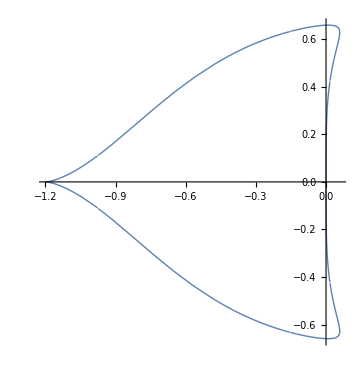
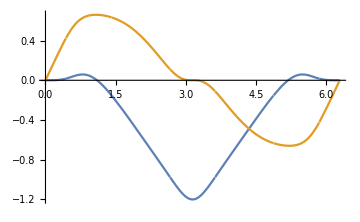
{-Graphics- -Graphics-,Null}

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
k=3;o=3;
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{bs,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
sol[[2]]
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b]
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
Print["C"->Subscript[C, o+1]/σ[1]]
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

```mathematica
1/1.2
```

0.833333

```mathematica
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

```mathematica
o=5;
Table[{Remove[R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{bs,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
sol[[2]];
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b];
Print["Stability interval length"->Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π]
(*错误系数C 计算*)
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
Print["C"->Subscript[C, o+1]/σ[1]]},{k,5,30}]
```

Set::wrsym: Symbol C is Protected.

C→26.812384259259259259260976053248436447370473653

Remove::remal: Symbol Removed[R] already removed.

Remove::remal: Symbol Removed[f] already removed.

Remove::remal: Symbol Removed[bs] already removed.

General::stop: Further output of Remove::remal will be suppressed during this calculation.

Set::wrsym: Symbol C is Protected.

C→85.499544452985778061696285081052307274042790054

Set::wrsym: Symbol C is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

C→226.52028804495050648031979007836476586341694684

C→524.768120859917318366182808281446225774640172416

C→1097.9412250543782929264268608149909214304565781

C→2120.5391021324790382132159463597174374362828863

C→3839.8591007801246291451462288776032389321491259

C→6593.9929055805146613994542215491134789056803567

C→10838.646834720505270670969141064671597692150875

C→17155.560552937607034218898075810590928671509939

C→26242.03492562899875006366425157342880860105373

C→39074.103944856356777158918511092174459326314452

C→56790.65803955984117432506020114738257369595156

C→80682.21636331743025413120892583374710061329455

C→112579.3120979856947599992496475021333071866178

C→154263.753504187698728997626966638724413415063

C→208023.839026288100588013291552943839258862458

C→276581.331001728619682681765798939952637098155

C→362853.04545136696822705006814771470521911396986

C→471044.317052755118626809412862458937914352865

C→604133.3239786083113143339336163587964751743

C→768178.967008898052512965644245020963800846538

C→967364.434513505387197579167430881431980851823

C→1.20796932478830847840357550236984186498839751×10^6

C→1.49571313768784272816363628015924262555625394×10^6

C→1.83901852158741310364002845362173409944241122×10^6

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

```mathematica
Table[{Remove[o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
o=1;
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
result=Table[{(2(k-i)+1)/(k+1)^2},{i,0,k}];
σ[ξ_]:=∑_(i=0)^k result[[i+1,1]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[i+1,1]]*i^o);
C=Subscript[C, o+1]/σ[1];
Print["C"->N[Subscript[C, o+1]/σ[1]]]},{k,1,2}]
```

Set::wrsym: Symbol C is Protected.

C→0.25

Remove::remal: Symbol Removed[o] already removed.

Remove::remal: Symbol Removed[R] already removed.

Remove::remal: Symbol Removed[f] already removed.

General::stop: Further output of Remove::remal will be suppressed during this calculation.

Set::wrsym: Symbol C is Protected.

C→1.94444

{{Null},{Null}}

```mathematica
N[53361/62]
```

860.661

```mathematica
o=3;
Table[{Remove[R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{bs,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
(*sol[[2]];*)
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b];
Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π}
,{k,3,30}]
```

Remove::remal: Symbol Removed[R] already removed.

Remove::remal: Symbol Removed[f] already removed.

Remove::remal: Symbol Removed[bs] already removed.

General::stop: Further output of Remove::remal will be suppressed during this calculation.

{{-1.20000001355366451807234553817226228958},{-1.79377933434868599817661638284506285393616707596},{-2.3478260869565217391304425205186636388483888815},{-2.877558710633066585672599481137396663742561975},{-3.3916899757972081984682932600048732246555860669},{-3.8952902196076472214486359631198936831310523366},{-4.391469108714782398348510916401176746186287562},{-4.8822291242794450700580444652341296689235518691},{-5.3689146779264236756269879439940476127099235403},{-5.852460688742897485923994771812761676108328526},{-6.333536963555962728892125811329327023361467286},{-6.8126357281138847749989873732186514452859292999},{-7.290126715681011537317584453749475159414990233},{-7.766292986270953064953543501810880979698313321},{-8.2413548902822920222616139588558504021045353782},{-8.715486507686976351274040652161838671208058197},{-9.1888271784979460602733603577463334950951182},{-9.661489751664456148967424117240006030328297541},{-9.839556915097827229987171101592723475527254887},{-10.60513402276324023520910516074608991920219835},{-11.07625566451399461204311494902921054377286913},{-8.861681108877430575134053486831786991418855202},{-12.0173671731670216517997337795406561027595971},{-12.4874408184529414813335493892114671851313408},{-11.8969512744182439063138503953084213905601341},{-13.42679003874885626434587637898398061049918154},{-13.896118790764650536541020589547199002994955},{-14.36524670781412488892338749629030309687951202}}

```mathematica
Table[2(k+1),{k,1,30}]
```

{4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62}

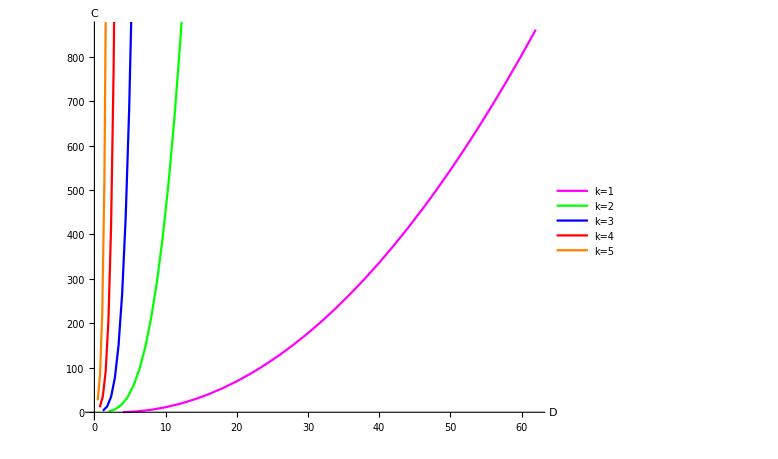

```mathematica
data1=
{{4,0.25},
{6,1.9444},
{8,5.625},
{10,11.3},
{12,18.9722},
{14,28.64286},
{16,40.3125},
{18,53.98148},
{20,69.65},
{22,87.31818},
{24,106.98611},
{26,128.65385},
{28,152.32143},
{30,177.98889},
{32,205.65625},
{34,235.32353},
{36,266.99074},
{38,300.65789},
{40,336.325},
{42,373.99206},
{44,413.65909},
{46,455.32609},
{48,498.99306},
{50,544.66},
{52,592.32692},
{54,641.99383},
{56,693.66071},
{58,747.32759},
{60,802.99444},
{62,860.66129}};
p1=ListLinePlot[data1,PlotRange->All,ImageSize->Large,AspectRatio->0.8,LabelStyle->{16,GrayLevel[0]},AxesOrigin->{0,0},AxesLabel->{Style[D,Medium],Style[C,Medium]},PlotLegends->{"k=1"},PlotStyle->{Magenta}];
data2={{2,2},
{2.9142135623730950488016889884830546450933948638033089677493`47.639980951469646,6.7045},
{3.7888543865742738425921615298184353285272179604851728431883`48.167499041465426,16.5207},
{4.6427344100918363913699284553411631559237403384136984887546`47.1059699672774,33.4461},
{5.4844769594540632154539593223124225412530146126360211552435`47.814521922939285,59.4801},
{6.3185355922720450889146982764304618057982663154535025729577`46.88374804899894,96.62227},
{7.1474305505614129836633086318750348451634078154765706565427`47.48332391797806,146.87258},
{7.9726916378122801945698734143960188422270306848492630837284`46.425222602311706,212.23092},
{8.7953000143105870648589943762433564943407866232536217416804`47.30926134077224,294.69728},
{9.6159134234968395709033604037298846788391409446987577544671`46.18191087905713,396.27161},
{10.4349890876313470757198827863919932478212508065517805411341`47.16681748953153,518.95391},
{11.2528546058530215685363049625161572918507485178529665807769`46.07515271088844,664.74415},
{12.0697507957032301869349415704164189756544465218073345631615`47.10219910051866,835.64235},
{12.8858586149771822245916757984873120436589796647533195676884`45.88606447736945,1033.64848},
{13.7013166561750297641330232091219375541942657722915582275652`46.98968354335862,1260.76256},
{14.5162328493177645956166631679569338611679452985039968578334`45.65609798465217,1518.98457},
{15.3306924913786785075411884006088396396495691009869104667764`46.8431461740479,1810.31452},
{16.1447638797588495697394167188857624716825242249512622556163`45.51742642681526,2136.7524},
{16.9585023438914455183427751834931687872068428865994061988674`46.75806060426664,2500.2982},
{17.7719531820474138726961718868620774598404466340167674746527`45.39478846381187,2902.95195},
{18.5851538350005542014080800474694803441047534008995444525667`46.71971891325042,3346.71362},
{19.3981355182005280987754675859874533596717286039173315655444`45.331671520188934,3833.58322},
{20.2109244634916082794103975491939521456507381732606696942808`46.645845605890024,4365.56075},
{21.023542875131349609820216930776695128513560382929913700914`45.22449177261395,4944.64621},
{21.83600967394118841246484860260017226973625977472811566454`46.54386750761429,5572.8396},
{22.6483410823987583929194314273624316422352001238290563442085`45.080317576302996,6252.14091},
{23.4605510889598380690187447131046933113215483577230854738577`46.48296007158614,6984.55016},
{24.2726518197178350430153256206831304346728407757998316448251`44.991342083528565,7772.06733},
{25.0846538382749361382557802326966562966600687743566432782325`46.42600668990478,8616.69243}};
p2=ListLinePlot[data2,PlotRange->All,ImageSize->Large,AspectRatio->0.8,LabelStyle->{16,GrayLevel[0]},AxesOrigin->{0,0},AxesLabel->{Style[D,Medium],Style[C,Medium]},PlotLegends->{"k=2"},PlotStyle->{Green}];
data3={{1.200000013553664518072345538172262289584174490940738263032`39.59878537341178,3.45833},{1.79377933434868599817661638284506285393616707595802556437889378455412691008325`48.51416110235576,13.06062},{2.3478260869565217391304425205186636388483888814929795022268`47.33713817999116,35.15278},{2.8775587106330665856725994811373966637425619746570426363491`46.86235748877733,77.70193},{3.3916899757972081984682932600048732246555860668789239823636`47.91186356369405,150.67415},{3.8952902196076472214486359631198936831310523365685488427666`47.28762717795429,266.03517},{4.3914691087147823983485109164011767461862875621196878042987`46.76761330969451,437.75054},{4.8822291242794450700580444652341296689235518691162755415689`47.13021184006434,681.78572},{5.3689146779264236756269879439940476127099235402762615572271`47.19374548629556,1016.10615},{5.8524606887428974859239947718127616761083285263427639266348`46.34146941765927,1460.67722},{6.3335369635559627288921258113293270233614672864073303021783`46.97656140367551,2037.46431},{6.8126357281138847749989873732186514452859292998977295814651`47.34650395331683,2770.4328},{7.2901267156810115373175844537494751594149902329871773153788`46.86027541519312,3685.54806},{7.7662929862709530649535435018108809796983133210424782306223`46.30263771499756,4810.77545},{8.2413548902822920222616139588558504021045353782008291039643`47.135096431330304,6176.08031},{8.7154865076869763512740406521618386712080581966851641181897`46.90508429529283,7813.42801},{9.1888271784979460602733603577463334950951182037407518481878`45.09974758894139,9756.78391},{9.6614897516644561489674241172400060303282975414303604733017`46.84789703258524,12042.11334},{9.839556915097827229987171101592723475527254887259244853904`46.01124359814536,14712.46066},{10.6051340227632402352091051607460899192021983498072488890745`46.24812247347134,17792.55424},{11.0762556645139946120431149490292105437728691347412333054766`46.22939295921709,21339.5964},{8.8616811088774305751340534868317869914188552018452777419874`46.42918058278913,25446.83873},{12.0173671731670216517997337795406561027595971045871240740088`46.19295544549952,29997.15088},{12.4874408184529414813335493892114671851313407502964697384866`45.81838273522615,35201.59390},{11.8969512744182439063138503953084213905601340967008359600731`45.363973764055686,41082.55407},{13.426790038748856264345876378983980610499181543154434224468`46.28492637526888,47611.63822},{13.8961187907646505365410205895471990029949549932527009750476`44.61963043180283,54923.17022},{14.3652467078141248889233874962903030968795120225852214731993`46.1619145273858,63046.32924}};
p3=ListLinePlot[data3,PlotRange->All,ImageSize->Large,AspectRatio->0.8,LabelStyle->{16,GrayLevel[0]},AxesOrigin->{0,0},AxesLabel->{Style[D,Medium],Style[C,Medium]},PlotLegends->{"k=3"},PlotStyle->{Blue}];
data4={{0.74999999999999999999999999999999999999999999999999999613275942890152751968566`48.380160215502656,11.14861},{1.1818977119893597584709270929201676477212344855894676345131`47.848199609194964,35.57864},{1.58680310399564246571144297269317391637683003070238483328906743949306989614398`48.35780827151739,92.4804},{1.9709165613916009435283118605299739982743374908198412536526`47.297282240474054,207.42509},{2.3399834073481908220231959775089875326490122524269218764846`47.89279035470409,416.9955},{2.6980870990232562815227494728409744222917043504209776413384`47.24179952419624,770.78569},{3.0480381535085174187870946016963553734962241013031637120361`47.13844196721911,1333.40092},{3.391791564108414780429074345438311883397314668631199104273`46.692820551540045,2186.45756},{3.7307356178368555096691983501296259979199005013558334668379`47.642348164072885,3430.5831},{4.0658782436591130039277817335954416173456598555960244878182`46.72103964482111,5187.41612},{4.3979667844728652517067851939252860063095200462367445111707`45.98095078109107,7601.6061},{4.7275661244533632859527138518490870580606549876909127018162`46.29919719902049,10842.81444},{5.0551106937346519761021371156999141407794607569118984620671`47.39440124314007,15107.7124},{5.3809398264640688828806138639989433868378837703373734867828`46.323972784804624,20621.98312},{5.7053222983014411278900478376594307482160710309483717505597`45.96880078893606,27642.32068},{6.0284736843446207531094821774284004894559285489171557040597`46.16295546914202,36458.4302},{6.2743536391814387111203453660457958222390076539541587254985`46.64105403277595,47388.02796},{6.6717511345409593096389477967901881339855632296923014599422`46.03071142490595,60813.84116},{6.9921189431110771746699201560876881513864812204460046382383`46.78339269963126,77115.63669},{6.1982478184243052750289581654940090924859826932417424736218`46.48047626379095,96662.69402},{5.466782072856917371173856796268918633810070393055992262402`46.264220994569534,120037.90473},{7.9494502102039710457670727802828352760117555305719854791429`45.66074764791308,147953.18379},{8.2665140138465583114060096825606415342559625068372928515318`46.49209054698827,180643.39985},{8.3635723341421939097929378447539427811723928329035828735288`46.28854329270374,218865.95681},{6.6679463156186920700561881801417193840831423315775968385236`46.30437038673486,263143.9612},{4.7135535297795520781076365268921475149110888755076207524963`46.708170659417924,314392.53864},{4.9822485719789688106146363560870932866197134578168555484502`46.164879636789166,373290.65812}};
p4=ListLinePlot[data4,PlotRange->All,ImageSize->Large,AspectRatio->0.8,LabelStyle->{16,GrayLevel[0]},AxesOrigin->{0,0},AxesLabel->{Style[D,Medium],Style[C,Medium]},PlotLegends->{"k=4"},PlotStyle->{Red}];
data5={{0.4691572545612510860127457904982333055429926462380509300583664841380209431299`48.35579438756068,26.81238},{0.79236202899576695138085833580672436133983333792685393025090538719171862525939`48.01974439254598,85.49954},{1.1054985036026664714207195649528029848437236919132817317919`47.44504199261,226.52029},{1.40515111761521295077746201532978891799471124773501613681693935620681777323554`48.20227749484891,524.76812},{1.6928850486642386737901082945452434584311942425899110920097`47.72872694817554,1097.94123},{1.970924881072185912752506781322980924617294332228818945331`47.402728051730364,2120.5391},{2.2412239130085247956658868519494337640383346553796122684182`47.27484992170377,3839.8591},{2.5053340483902155519405794105171966169638456377944485149832`47.12121025239216,6593.99291},{2.4128880030441143861569136511120710814131989487860699014257`47.266345566515334,10838.64683},{2.2471459090287265953965204998676303814672236337144480335734`46.98179938044124,17155.56055},{3.271235935811240641699940989624875924124616295397717754894`46.278409966281096,26242.03493},{3.5201764897405716026065957115067753362298900580469654825859`46.90568499296734,39074.10394},{3.2538504363302198998779923880841205641060959360598725775355`45.84529020826838,56790.65804},{4.011418588109012229915583222605162754514866064693367684986`46.37333659271878,80682.21636},{1.6704316730593065373425893707267774076892543390165552638805`46.10719423875476,112579.31211},{0.7480290592844183702984306306380864567728330731976197322636`45.461276665313044,154263.7535},{0.7401630305631016114566122744921780750815175623248451816011`46.22479927163034,208023.83903},{0.8774686032044508954071017616507185430096084971592190308137`45.64212007277775,276581.331},{3.8081034178496534926956263112369291707812232304544319609096`46.96456390719893,362853.04545},{0.983566991922309024813140763919224510552712299556475020266`46.238955740578476,471044.31705},{5.687357185439274533788992793581393528635915479840817439296`43.35019986329339,604133.32398},{0.4642852832202037398901446057590369903106411470253135434586`46.61239650431029,768178.96701},{0.3814116339513366102223645870732220084679331529209645337189`46.70215376942631,967364.43451},{0.4547136122642185604549461597411560270297251288767390917609`46.332728986093095,1207969.32479},{0.2093557977548726477963204996977958609436084848297240940148`46.95983360764658,1495713.13769},{0.4721572171670786928854881180547101762789882855553020866797`46.59627337461695,1839018.52159}};
p5=ListLinePlot[data5,PlotRange->All,ImageSize->Large,AspectRatio->0.8,LabelStyle->{16,GrayLevel[0]},AxesOrigin->{0,0},AxesLabel->{Style[D,Medium],Style[C,Medium]},PlotLegends->{"k=5"},PlotStyle->{Orange}];
Show[p1,p2,p3,p4,p5]
```

```mathematica
o=4;
Table[{Remove[R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{bs,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
(*sol[[2]];*)
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b];
Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π}
,{k,4,30}]
```

Remove::remal: Symbol Removed[R] already removed.

Remove::remal: Symbol Removed[f] already removed.

Remove::remal: Symbol Removed[bs] already removed.

General::stop: Further output of Remove::remal will be suppressed during this calculation.

{{-0.75},{-1.1818977119893597584709270929201676477212344856},{-1.5868031039956424657114429726931739163768300307},{-1.9709165613916009435283118605299739982743374908},{-2.3399834073481908220231959775089875326490122524},{-2.6980870990232562815227494728409744222917043504},{-3.0480381535085174187870946016963553734962241013},{-3.391791564108414780429074345438311883397314669},{-3.7307356178368555096691983501296259979199005014},{-4.065878243659113003927781733595441617345659856},{-4.39796678447286525170678519392528600630952005},{-4.727566124453363285952713851849087058060654988},{-5.0551106937346519761021371156999141407794607569},{-5.38093982646406888288061386399894338683788377},{-5.70532229830144112789004783765943074821607103},{-6.028473684344620753109482177428400489455928549},{-6.274353639181438711120345366045795822239007654},{-6.67175113454095930963894779679018813398556323},{-6.99211894311107717466992015608768815138648122},{-6.198247818424305275028958165494009092485982693},{-5.466782072856917371173856796268918633810070393},{-7.94945021020397104576707278028283527601175553},{-8.266514013846558311406009682560641534255962507},{-8.363572334142193909792937844753942781172392833},{-6.667946315618692070056188180141719384083142332},{-4.713553529779552078107636526892147514911088876},{-4.982248571978968810614636356087093286619713458}}

```mathematica
o=5;
Table[{Remove[R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{bs,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
(*sol[[2]];*)
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b];
Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π}
,{k,5,30}]
```

Remove::remal: Symbol Removed[R] already removed.

Remove::remal: Symbol Removed[f] already removed.

Remove::remal: Symbol Removed[bs] already removed.

General::stop: Further output of Remove::remal will be suppressed during this calculation.

{{-0.469157254561251086012745790498233305542992646238},{-0.792362028995766951380858335806724361339833337927},{-1.1054985036026664714207195649528029848437236919},{-1.40515111761521295077746201532978891799471124774},{-1.6928850486642386737901082945452434584311942426},{-1.9709248810721859127525067813229809246172943322},{-2.2412239130085247956658868519494337640383346554},{-2.5053340483902155519405794105171966169638456378},{-2.4128880030441143861569136511120710814131989488},{-2.247145909028726595396520499867630381467223634},{-3.271235935811240641699940989624875924124616295},{-3.520176489740571602606595711506775336229890058},{-3.25385043633021989987799238808412056410609594},{-4.011418588109012229915583222605162754514866065},{-1.670431673059306537342589370726777407689254339},{-0.748029059284418370298430630638086456772833073},{-0.7401630305631016114566122744921780750815175623},{-0.877468603204450895407101761650718543009608497},{-3.80810341784965349269562631123692917078122323},{-0.9835669919223090248131407639192245105527122996},{-5.687357185439274533788992793581393528635915},{-0.464285283220203739890144605759036990310641147},{-0.3814116339513366102223645870732220084679331529},{-0.4547136122642185604549461597411560270297251289},{-0.2093557977548726477963204996977958609436084848},{-0.4721572171670786928854881180547101762789882856}}

```mathematica
k3o3={{0.125,Log[10,2084614.5229416459333]},{0.125,Log[10,2084614.5229416459333]},{0.11111111111111110494,Log[10,12668670.595602445304]},{0.11111111111111110494,Log[10,12668670.595602445304]},{0.10000000000000000555,Log[10,65954210.190280847251]},{0.10000000000000000555,Log[10,65954210.190280847251]},{0.090909090909090911614,Log[10,298742911.88131964207]},{0.083333333333333328707,Log[10,1191784985.785492897]},{0.083333333333333328707,Log[10,1191784985.785492897]},{0.076923076923076927347,Log[10,4228673249.9869656563]},{0.071428571428571424606,Log[10,13452333336.956912994]},{0.066666666666666665741,Log[10,38624251362.95489502]},{0.0625,Log[10,100646973149.82830811]},{0.058823529411764705066,Log[10,239138015909.86035156]},{0.055555555555555552472,Log[10,520140972475.61541748]},{0.052631578947368418131,Log[10,1039142285357.0955811]},{0.050000000000000002776,Log[10,1912257556559.2902832]},{0.047619047619047616404,Log[10,3249228076937.0634766]},{0.045454545454545455807,Log[10,5108035289503.2626953]},{0.043478260869565216185,Log[10,7442095062500.359375]},{0.041666666666666664354,Log[10,10062266794205.386719]},{0.040000000000000000833,Log[10,12639250089935.492188]},{0.038461538461538463674,Log[10,14761077847734.568359]},{0.037037037037037034981,Log[10,16036794127622.140625]},{0.034482758620689654694,Log[10,15250438092217.875]},{0.033333333333333332871,Log[10,13345554746395.09375]},{0.032258064516129031363,Log[10,10858287171776.625]},{0.030303030303030303871,Log[10,5755397145739.1230469]},{0.029411764705882352533,Log[10,3738942968579.6787109]},{0.028571428571428570536,Log[10,2245513801160.2021484]},{0.027777777777777776236,Log[10,1243538429711.340332]},{0.026315789473684209065,Log[10,294957802966.67687988]},{0.025641025641025640136,Log[10,125203656862.17770386]},{0.025000000000000001388,Log[10,48110043998.351226807]},{0.023809523809523808202,Log[10,5092183098.0289707184]},{0.02325581395348837177,Log[10,1369501706.2493691444]},{0.02222222222222222307,Log[10,61508377.202391728759]},{0.021739130434782608092,Log[10,9614118.8890189100057]},{0.020833333333333332177,Log[10,89395.558774325210834]},{0.020000000000000000416,Log[10,13.373440074370835262]},{0.019607843137254901689,Log[10,0.96136954778978611635]},{0.018867924528301886072,Log[10,0.17858442221154940954]},{0.018181818181818180935,Log[10,0.005401085897907292703]},{0.017543859649122806044,Log[10,0.0092190626636285306905]},{0.016949152542372881297,Log[10,0.002601841216339360191]},{0.016393442622950820525,Log[10,0.0005548649168218592817]},{0.015873015873015872135,Log[10,0.00010632788932247603988]},{0.015151515151515151936,Log[10,1.3717188294360329329*10^-5]},{0.014705882352941176267,Log[10,3.1429904740841630803*10^-6]},{0.014084507042253521444,Log[10,1.2948296829170929144*10^-7]},{0.013698630136986300609,Log[10,2.5871825985855567988*10^-8]},{0.013157894736842104533,Log[10,5.1756789354697326779*10^-9]},{0.012820512820512820068,Log[10,9.3828845095924061305*10^-10]},{0.012345679012345678327,Log[10,4.1981156977320293201*10^-11]},{0.011904761904761904101,Log[10,4.3697230742211886951*10^-12]},{0.011494252873563218231,Log[10,2.5263441046935704815*10^-13]},{0.011111111111111111535,Log[10,1.3852541831355793677*10^-14]},{0.010752688172043011611,Log[10,1.0723716167142245408*10^-15]},{0.010309278350515463721,Log[10,2.3284534307255758938*10^-17]},{0.010000000000000000208,Log[10,3.3438863518946208511*10^-19]},{0.0097087378640776690608,Log[10,5.7243511078894232538*10^-20]},{0.0093457943925233637888,Log[10,8.8459051623584512511*10^-22]},{0.0090090090090090089309,Log[10,1.2081862734455767824*10^-23]},{0.0086956521739130435839,Log[10,1.4684532619738553114*10^-25]},{0.0084033613445378147616,Log[10,1.6295574292053556119*10^-27]},{0.0081300813008130089904,Log[10,2.6297123622373004149*10^-29]},{0.0078740157480314959537,Log[10,3.4185361324055696133*10^-30]},{0.0075757575757575759678,Log[10,7.9204407225231786254*10^-31]},{0.0072992700729927004893,Log[10,2.0504785052447693419*10^-31]},{0.0070422535211267607222,Log[10,5.6714778808749501378*10^-32]},{0.0068027210884353738959,Log[10,1.6718323833047777733*10^-32]},{0.0065789473684210522664,Log[10,5.2373489805787812051*10^-33]},{0.0063694267515923570083,Log[10,1.7387641021454506825*10^-33]},{0.0061349693251533743768,Log[10,4.9797442194653820329*10^-34]},{0.0059523809523809520505,Log[10,1.8606780693641520427*10^-34]},{0.0057471264367816091156,Log[10,6.0947080621943595224*10^-35]},{0.005524861878453038444,Log[10,1.8037055350982422021*10^-35]},{0.005347593582887700224,Log[10,6.7978158853379100521*10^-36]},{0.0051546391752577318604,Log[10,2.343912819044318976*10^-36]},{0.0050000000000000001041,Log[10,9.981340029129374117*10^-37]},{0.0048309178743961350352,Log[10,3.930306883349112011*10^-37]},{0.0046511627906976743541,Log[10,1.4647277281817656054*10^-37]},{0.0045045045045045044654,Log[10,6.5769306969078506991*10^-38]},{0.0043478260869565217919,Log[10,2.8138744338778616471*10^-38]},{0.0042016806722689073808,Log[10,1.2843102101700827778*10^-38]},{0.0040485829959514170462,Log[10,5.7020005263854368371*10^-39]},{0.0039215686274509803377,Log[10,2.9330176588234704995*10^-39]},{0.0037735849056603773879,Log[10,1.3678580640213637702*10^-39]},{0.0036496350364963502447,Log[10,7.3004190173877984085*10^-40]},{0.0035211267605633803611,Log[10,3.8526933773142665915*10^-40]},{0.003401360544217686948,Log[10,2.1489884627957965922*10^-40]},{0.0032894736842105261332,Log[10,1.2597214026793099739*10^-40]},{0.0031746031746031746004,Log[10,7.3690129518265621105*10^-41]},{0.0030674846625766871884,Log[10,4.5226056914187931314*10^-41]},{0.0029673590504451039657,Log[10,2.8968975065904214884*10^-41]},{0.0028653295128939827198,Log[10,1.8608592546052358544*10^-41]},{0.002762430939226519222,Log[10,1.2052574477775188918*10^-41]},{0.002673796791443850112,Log[10,8.3740109418158785111*10^-42]},{0.0025773195876288659302,Log[10,5.6946498838847779855*10^-42]},{0.0024937655860349126555,Log[10,4.1155908928715707951*10^-42]},{0.002409638554216867682,Log[10,2.9937375323971624755*10^-42]},{0.002325581395348837177,Log[10,2.1973872739646279782*10^-42]},{0.002247191011235955254,Log[10,1.659788564289088058*10^-42]},{0.0021691973969631237092,Log[10,1.2648123572633548198*10^-42]},{0.0020964360587002097563,Log[10,9.8796880363945008904*10^-43]},{0.0020242914979757085231,Log[10,7.7800867445898772126*10^-43]},{0.0019569471624266143728,Log[10,6.2573846733441527876*10^-43]},{0.001886792452830188694,Log[10,5.0126991329128793657*10^-43]},{0.0018248175182481751223,Log[10,4.1377312218540064702*10^-43]},{0.0017605633802816901805,Log[10,3.4043885281856728491*10^-43]},{0.001700680272108843474,Log[10,2.847602253364581558*10^-43]},{0.0016447368421052630666,Log[10,2.4162213344469262754*10^-43]},{0.0015873015873015873002,Log[10,2.0459678448228892041*10^-43]},{0.0015337423312883435942,Log[10,1.7552803724269928684*10^-43]},{0.0014814814814814814079,Log[10,1.5137490920867894926*10^-43]},{0.0014306151645207439149,Log[10,1.312149708991084354*10^-43]},{0.001381215469613259611,Log[10,1.1430751700878066253*10^-43]},{0.0013351134846461948889,Log[10,1.0055382892442986566*10^-43]},{0.0012886597938144329651,Log[10,8.8394543774687069859*10^-44]},{0.0012453300124533001145,Log[10,7.8386006920648748091*10^-44]},{0.0012033694344163658671,Log[10,6.976396022769740382*10^-44]},{0.0011614401858304297319,Log[10,6.2072717314317679966*10^-44]},{0.0011223344556677890965,Log[10,5.5635850010977209695*10^-44]},{0.0010845986984815618546,Log[10,5.0024052740853563858*10^-44]},{0.0010471204188481676462,Log[10,4.4972410275257934631*10^-44]},{0.0010111223458038423074,Log[10,4.0560789909044088725*10^-44]},{0.0009765625,Log[10,3.6692468509721391269*10^-44]},{0.00094339622641509434699,Log[10,3.3287433819537145978*10^-44]},{0.00091157702825888785488,Log[10,3.0279194683792923522*10^-44]},{0.00088028169014084509027,Log[10,2.7547108015342783747*10^-44]},{0.00085034013605442173699,Log[10,2.5127107889935338045*10^-44]},{0.0008216926869350862396,Log[10,2.2975972356866098684*10^-44]},{0.00079365079365079365011,Log[10,2.1014884159292203154*10^-44]},{0.00076628352490421458489,Log[10,1.9229567140727907932*10^-44]},{0.00074019245003700958815,Log[10,1.763815319826680875*10^-44]},{0.00071530758226037195746,Log[10,1.6214803597227555307*10^-44]},{0.0006906077348066298055,Log[10,1.4887977494349818633*10^-44]},{0.00066711140760506999325,Log[10,1.370089088403725072*10^-44]},{0.00064432989690721648255,Log[10,1.2616150613032667535*10^-44]},{0.00062266500622665005727,Log[10,1.1642079999629470776*10^-44]},{0.00060132291040288637918,Log[10,1.0734755545368490077*10^-44]},{0.00058072009291521486593,Log[10,9.9058433859971634924*10^-45]},{0.00056116722783389454826,Log[10,9.1600520807994782826*10^-45]},{0.00054200542005420054154,Log[10,8.4662510801534419954*10^-45]},{0.00052356020942408382311,Log[10,7.8317495894956738082*10^-45]},{0.00050556117290192115372,Log[10,7.2429966448081020747*10^-45]},{0.00048828125,Log[10,6.7050521351673771811*10^-45]},{0.00047169811320754717349,Log[10,6.2131209093152356182*10^-45]},{0.00045578851412944392744,Log[10,5.7628782791967694347*10^-45]},{0.00044014084507042254514,Log[10,5.3401873517803399559*10^-45]},{0.0004251700680272108685,Log[10,4.9539666272650364971*10^-45]},{0.0004106776180698151887,Log[10,4.5965881251835197542*10^-45]},{0.00039666798889329631279,Log[10,4.2661718111946169016*10^-45]},{0.00038314176245210729245,Log[10,3.9608767152399532388*10^-45]},{0.00037009622501850479408,Log[10,3.6789226679284187789*10^-45]},{0.000357525920629245611,Log[10,3.4186054769470268547*10^-45]},{0.00034530386740331490275,Log[10,3.1759884916559744262*10^-45]},{0.00033355570380253499662,Log[10,2.9523477297867463072*10^-45]},{0.00032216494845360824128,Log[10,2.7443121800951237124*10^-45]},{0.00031123560535325242669,Log[10,2.5527173101100387169*10^-45]},{0.00030066145520144318959,Log[10,2.3747040905671548923*10^-45]},{0.00029036004645760743297,Log[10,2.2081377364401796434*10^-45]},{0.00028050490883590464223,Log[10,2.0550332062820950822*10^-45]},{0.00027092928745597400289,Log[10,1.9120458634757611818*10^-45]},{0.00026171159382360636471,Log[10,1.7797145137560009424*10^-45]},{0.00025278058645096057686,Log[10,1.656411448924021829*10^-45]},{0.000244140625,Log[10,1.5416779981804254243*10^-45]},{0.00023584905660377358675,Log[10,1.4357369696828000959*10^-45]},{0.00022784233310549099004,Log[10,1.3372706145713156786*10^-45]},{0.00022007042253521127257,Log[10,1.2452634200401125631*10^-45]},{0.00021253985122210414835,Log[10,1.1594407021559943434*10^-45]},{0.00020533880903490759435,Log[10,1.0804118841282370115*10^-45]},{0.0001983339944466481564,Log[10,1.006365033654956048*10^-45]},{0.00019157088122605364622,Log[10,9.3750086997814608425*10^-46]},{0.00018504811250925239704,Log[10,8.7351299412446583968*10^-46]},{0.00017873100983020553142,Log[10,8.1380162427160340047*10^-46]},{0.00017265193370165745138,Log[10,7.5842622215134946656*10^-46]},{0.00016677785190126749831,Log[10,7.0685078147294428069*10^-46]},{0.00016108247422680412064,Log[10,6.5864834964304104959*10^-46]},{0.00015559358954411078076,Log[10,6.1386570847265269613*10^-46]},{0.00015030813166992334855,Log[10,5.7228652953997232891*10^-46]},{0.00014518002322880371648,Log[10,5.333862747907872307*10^-46]},{0.00014023278642546626064,Log[10,4.9719744083026432959*10^-46]},{0.00013544629554381688104,Log[10,4.6343133379363055964*10^-46]},{0.00013083867591259977178,Log[10,4.3208105908779592466*10^-46]},{0.00012639029322548028843,Log[10,4.0288438468050910257*10^-46]}};
k3o3=Table[{-Log[k3o3[[k,1]]],k3o3[[k,2]]},{k,1,Length[k3o3]}];
```

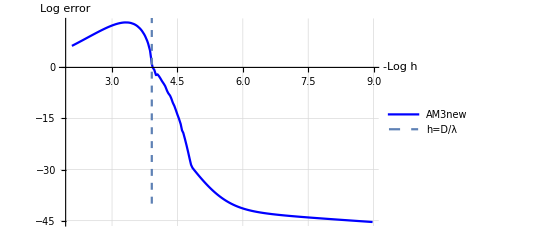

```mathematica
gk3o3=ListLinePlot[k3o3,Joined->True,PlotStyle->Blue,PlotLegends->{"AM3new"}];
Show[
gk3o3,ParametricPlot[{-Log[0.02],t},{t,-40,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
k=4;o=1;
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
co=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,2,2}];
```

```mathematica
bs^2
```

(r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)^2

```mathematica
cc=Expand[bs^2+co^2]
```

{1/4+r[0]^4+r[0] r[1]+3 r[0]^2 r[1]^2+r[1]^4+3 r[0] r[2]+r[1] r[2]+6 r[0]^2 r[1] r[2]+2 r[0] r[1]^2 r[2]+11 r[0]^2 r[2]^2+6 r[0] r[1] r[2]^2+3 r[1]^2 r[2]^2+r[2]^4+5 r[0] r[3]+3 r[1] r[3]+10 r[0]^2 r[1] r[3]+6 r[0] r[1]^2 r[3]+r[2] r[3]+30 r[0]^2 r[2] r[3]+30 r[0] r[1] r[2] r[3]+6 r[1]^2 r[2] r[3]+6 r[0] r[2]^2 r[3]+2 r[1] r[2]^2 r[3]+27 r[0]^2 r[3]^2+30 r[0] r[1] r[3]^2+11 r[1]^2 r[3]^2+10 r[0] r[2] r[3]^2+6 r[1] r[2] r[3]^2+3 r[2]^2 r[3]^2+r[3]^4+7 r[0] r[4]+5 r[1] r[4]+14 r[0]^2 r[1] r[4]+10 r[0] r[1]^2 r[4]+3 r[2] r[4]+42 r[0]^2 r[2] r[4]+50 r[0] r[1] r[2] r[4]+10 r[1]^2 r[2] r[4]+18 r[0] r[2]^2 r[4]+6 r[1] r[2]^2 r[4]+r[3] r[4]+70 r[0]^2 r[3] r[4]+94 r[0] r[1] r[3] r[4]+30 r[1]^2 r[3] r[4]+50 r[0] r[2] r[3] r[4]+30 r[1] r[2] r[3] r[4]+6 r[2]^2 r[3] r[4]+10 r[0] r[3]^2 r[4]+6 r[1] r[3]^2 r[4]+2 r[2] r[3]^2 r[4]+51 r[0]^2 r[4]^2+70 r[0] r[1] r[4]^2+27 r[1]^2 r[4]^2+42 r[0] r[2] r[4]^2+30 r[1] r[2] r[4]^2+11 r[2]^2 r[4]^2+14 r[0] r[3] r[4]^2+10 r[1] r[3] r[4]^2+6 r[2] r[3] r[4]^2+3 r[3]^2 r[4]^2+r[4]^4}

```mathematica
cons=Prepend[con,f]
(*r[i] решение*)
(*r[i] 求解*)
R
```

{r[0]+r[1]+r[2]+r[3]+r[4]==1}

{r[0],r[1],r[2],r[3],r[4]}

```mathematica
sol=NMinimize[{cc,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25]
```

NMinimize::objfs: The objective function {1/4+r[0]^4+r[0] r[1]+3 r[0]^2 r[1]^2+r[1]^4+3 r[0] r[2]+r[1] r[2]+6 r[0]^2 r[1] r[2]+2 r[0] r[1]^2 r[2]+11 r[0]^2 r[2]^2+«20»} should be scalar-valued.

NMinimize[{{1/4+r[0]^4+r[0] r[1]+3 r[0]^2 r[1]^2+r[1]^4+3 r[0] r[2]+r[1] r[2]+6 r[0]^2 r[1] r[2]+2 r[0] r[1]^2 r[2]+11 r[0]^2 r[2]^2+6 r[0] r[1] r[2]^2+3 r[1]^2 r[2]^2+r[2]^4+5 r[0] r[3]+3 r[1] r[3]+10 r[0]^2 r[1] r[3]+6 r[0] r[1]^2 r[3]+r[2] r[3]+30 r[0]^2 r[2] r[3]+30 r[0] r[1] r[2] r[3]+6 r[1]^2 r[2] r[3]+6 r[0] r[2]^2 r[3]+2 r[1] r[2]^2 r[3]+27 r[0]^2 r[3]^2+30 r[0] r[1] r[3]^2+11 r[1]^2 r[3]^2+10 r[0] r[2] r[3]^2+6 r[1] r[2] r[3]^2+3 r[2]^2 r[3]^2+r[3]^4},{r[0]+r[1]+r[2]+r[3]==1}},{r[0],r[1],r[2],r[3]},Method→Automatic,MaxIterations→250,WorkingPrecision→50,AccuracyGoal→25,PrecisionGoal→25]

```mathematica
bs^2+co^2
```

{(1/2+r[0] r[1]+3 r[0] r[2]+r[1] r[2]+5 r[0] r[3]+3 r[1] r[3]+r[2] r[3]+7 r[0] r[4]+5 r[1] r[4]+3 r[2] r[4]+r[3] r[4])^2+(r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)^2}

```mathematica
sol=NMinimize[{(1/2+r[0] r[1]+3 r[0] r[2]+r[1] r[2]+5 r[0] r[3]+3 r[1] r[3]+r[2] r[3]+7 r[0] r[4]+5 r[1] r[4]+3 r[2] r[4]+r[3] r[4])^2+(r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)^2,cons},R]
```

{0.266748,{r[0]→-0.215087,r[1]→0.0580519,r[2]→0.309017,r[3]→0.441948,r[4]→0.40607}}

{{β[0]→0.932562,β[1]→0.308595,β[2]→-0.125565,β[3]→-0.115592}}

Stability interval length→-3.25736

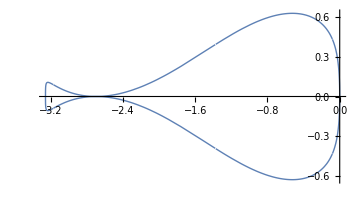
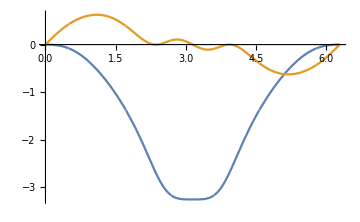
{-Graphics- -Graphics-,Null}

```mathematica
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b]
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

{{β[0]→0.826819,β[1]→0.406157,β[2]→0.0131888,β[3]→-0.158825,β[4]→-0.0873404}}

Set::wrsym: Symbol C is Protected.

C→16.3506

Stability interval length→-3.95777

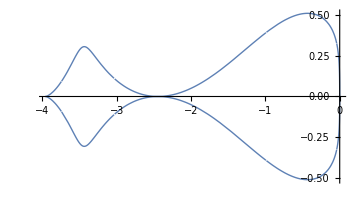
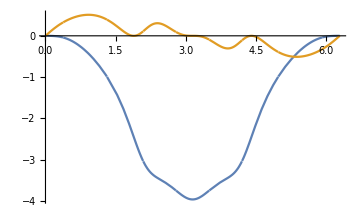
{-Graphics- -Graphics-,Null}

```mathematica
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result={{β[0]->0.8268191317713608,β[1]->0.4061570914666151,β[2]->0.013188754233130873,β[3]->-0.1588245730439245,β[4]->-0.08734040442718237}}
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
Print["C"->Subscript[C, o+1]/σ[1]]
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
k=4;o=2; (*两个条件 第三个加进去*)
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
co=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,2,o}];
cc=Expand[bs^2+co^2];
cons=Prepend[con,f];
```

{r[0]+r[1]+r[2]+r[3]+r[4]==1,r[0] r[1]+3 r[0] r[2]+r[1] r[2]+5 r[0] r[3]+3 r[1] r[3]+r[2] r[3]+7 r[0] r[4]+5 r[1] r[4]+3 r[2] r[4]+r[3] r[4]==-1/2}

```mathematica
Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,3,3}]
```

{-1/3+r[0] r[1]+5 r[0] r[2]+r[1] r[2]+13 r[0] r[3]+5 r[1] r[3]+r[2] r[3]+25 r[0] r[4]+13 r[1] r[4]+5 r[2] r[4]+r[3] r[4]}

```mathematica
bs^2+(%184)^2
```

{(-1/3+r[0] r[1]+5 r[0] r[2]+r[1] r[2]+13 r[0] r[3]+5 r[1] r[3]+r[2] r[3]+25 r[0] r[4]+13 r[1] r[4]+5 r[2] r[4]+r[3] r[4])^2+(r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)^2}

{{β[0]→1.38962,β[1]→-0.0107652,β[2]→-0.501658,β[3]→-0.022883,β[4]→0.145682}}

Stability interval length→-1.87389

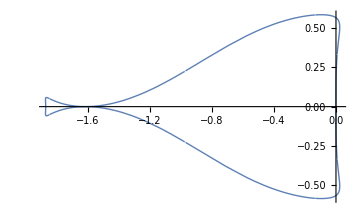
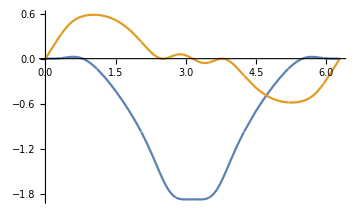
{-Graphics- -Graphics-,Null}

```mathematica
sol=NMinimize[{(-1/3+r[0] r[1]+5 r[0] r[2]+r[1] r[2]+13 r[0] r[3]+5 r[1] r[3]+r[2] r[3]+25 r[0] r[4]+13 r[1] r[4]+5 r[2] r[4]+r[3] r[4])^2+(r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)^2,cons},R];
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b]
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
k=4;o=1;  (*一个个条件 第二 三个加进去 o->3 *) 
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
co=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,2,o}];
cc=Expand[bs^2+co^2];
cons=Prepend[con,f];
```

```mathematica
Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,2,2}]+Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,3,3}]
```

{1/6+2 r[0] r[1]+8 r[0] r[2]+2 r[1] r[2]+18 r[0] r[3]+8 r[1] r[3]+2 r[2] r[3]+32 r[0] r[4]+18 r[1] r[4]+8 r[2] r[4]+2 r[3] r[4]}

```mathematica
bs^2+(%230)^2
```

{(1/6+2 r[0] r[1]+8 r[0] r[2]+2 r[1] r[2]+18 r[0] r[3]+8 r[1] r[3]+2 r[2] r[3]+32 r[0] r[4]+18 r[1] r[4]+8 r[2] r[4]+2 r[3] r[4])^2+(r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)^2}

{{β[0]→0.627363,β[1]→0.363721,β[2]→0.103799,β[3]→-0.0499219,β[4]→-0.0449609}}

Stability interval length→-5.37054

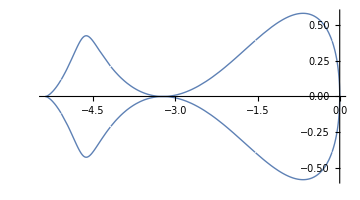
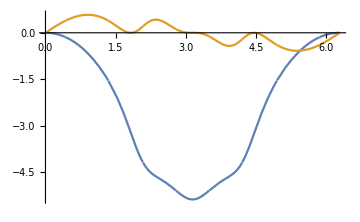
{-Graphics- -Graphics-,Null}

```mathematica
sol=NMinimize[{(1/6+2 r[0] r[1]+8 r[0] r[2]+2 r[1] r[2]+18 r[0] r[3]+8 r[1] r[3]+2 r[2] r[3]+32 r[0] r[4]+18 r[1] r[4]+8 r[2] r[4]+2 r[3] r[4])^2+(r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)^2,cons},R];
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b]
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

{r[0]→0.41893179952785617220017065020776865437287538921,r[1]→0.4499023538302249470534712737958600303619045946873,r[2]→0.30900500527047880191270928810177269928364187578863,r[3]→0.050095864562322880761753282405628144114436761836742,r[4]→-0.2279350231908828019281044945110295281328586215225}

{β[4]=={-0.0954892294407801614617980074691365208399964270757},β[3]=={-0.08156175276392739992765984401564835609579972115906+β[4]},β[2]=={0.0815572072624001329029045304489034496666221604269+β[3]-β[4]},β[1]=={0.331561752760753274814024380353515472427195363692+β[2]-β[3]+β[4]},β[0]=={0.5278640443631083073450578813647319096839572482317+β[1]-β[2]+β[3]-β[4]}}

Set::wrsym: Symbol C is Protected.

C→16.5207595331055698148046572298335711314091671097

Stability interval length→-3.78885438657427384259216152981843532852721796049

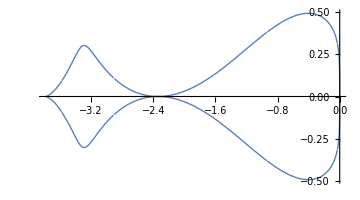
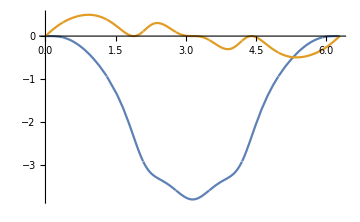
{-Graphics- -Graphics-,Null}

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
k=4;o=2;
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{bs,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
sol[[2]]
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]]
result=Solve[c,b];
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
Print["C"->Subscript[C, o+1]/σ[1]]
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

```mathematica
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
Print["C"->Subscript[C, o+1]/σ[1]]
```

Set::wrsym: Symbol C is Protected.

C→16.5207595331055698148046572298335711314091671097

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
k=4;o=2;
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{cc,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
sol[[2]]
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]]
result=Solve[c,b]
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
Print["C"->Subscript[C, o+1]/σ[1]]
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

NMinimize::objfs: The objective function {1/2+r[0]^2+r[0] r[1]+r[1]^2+3 r[0] r[2]+r[1] r[2]+r[2]^2+5 r[0] r[3]+3 r[1] r[3]+r[2] r[3]+«6»} should be scalar-valued.

{r[0],r[1],r[2],r[3],r[4]}

ReplaceAll::reps: {r[0],r[1],r[2],r[3],r[4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]}

ReplaceAll::reps: {r[0],r[1],r[2],r[3],r[4]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: {β[4]==r[0] r[4],β[3]==r[0] r[3]+r[1] r[4]+β[4],β[2]==r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4],β[1]==r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4],β[0]==r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}/.{r[0],r[1],r[2],r[3],r[4]} is not a quantified system of equations and inequalities.

Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]

Part::partw: Part 3 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

Part::partw: Part 4 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

Part::partw: Part 5 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

Part::partw: Part 4 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

Part::partw: Part 5 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::wrsym: Symbol C is Protected.

Part::partw: Part 3 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

Part::partw: Part 4 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

Part::partw: Part 5 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

C→(91-3 (4 Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,3,2⟧+9 Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,4,2⟧+16 Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,5,2⟧+r[1]))/(6 ((β[3]=={r[0] r[3]+r[1] r[4]+β[4]})+Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,3,2⟧+Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,4,2⟧+Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,5,2⟧+r[1]))

Part::partw: Part 3 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

Part::partw: Part 4 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

Part::partw: Part 5 of {β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {r[0.],r[1.],r[2.],r[3.],r[4.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: {β[4.]==r[0.] r[4.],β[3.]==r[0.] r[3.]+r[1.] r[4.]+β[4.],β[2.]==r[0.] r[2.]+r[1.] r[3.]+r[2.] r[4.]+β[3.]-1. β[4.],β[1.]==r[0.] r[1.]+r[1.] r[2.]+r[2.] r[3.]+r[3.] r[4.]+β[2.]-1. β[3.]+β[4.],β[0.]==r[0.]^2+r[1.]^2+r[2.]^2+r[3.]^2+r[4.]^2+β[1.]-1. β[2.]+β[3.]-1. β[4.]}/.{r[0.],r[1.],r[2.],r[3.],r[4.]} is not a quantified system of equations and inequalities.

ReplaceAll::reps: {r[0.],r[1.],r[2.],r[3.],r[4.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::naqs: {β[4.]==r[0.] r[4.],β[3.]==r[0.] r[3.]+r[1.] r[4.]+β[4.],β[2.]==r[0.] r[2.]+r[1.] r[3.]+r[2.] r[4.]+β[3.]-1. β[4.],β[1.]==r[0.] r[1.]+r[1.] r[2.]+r[2.] r[3.]+r[3.] r[4.]+β[2.]-1. β[3.]+β[4.],β[0.]==r[0.]^2+r[1.]^2+r[2.]^2+r[3.]^2+r[4.]^2+β[1.]-1. β[2.]+β[3.]-1. β[4.]}/.{r[0.],r[1.],r[2.],r[3.],r[4.]} is not a quantified system of equations and inequalities.

General::stop: Further output of Solve::naqs will be suppressed during this calculation.

Stability interval length→-2 Re[1/((β[3]=={r[0] r[3]+r[1] r[4]+β[4]})+Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,3,2⟧-Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,4,2⟧+Solve[{β[4]=={r[0] r[4]},β[3]=={r[0] r[3]+r[1] r[4]+β[4]},β[2]=={r[0] r[2]+r[1] r[3]+r[2] r[4]+β[3]-β[4]},β[1]=={r[0] r[1]+r[1] r[2]+r[2] r[3]+r[3] r[4]+β[2]-β[3]+β[4]},β[0]=={r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2+β[1]-β[2]+β[3]-β[4]}}/.{r[0],r[1],r[2],r[3],r[4]},{β[0],β[1],β[2],β[3],β[4]}]⟦1,5,2⟧-r[1])]

{-Graphics- -Graphics-,Null}

```mathematica
α=0.1;
part2=(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,2,2}])^2;
part3=(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,3,3}])^2;
coo=(1-α)*part3;
α*bs+coo
```

{0.9 (-1/3+r[0] r[1]+5 r[0] r[2]+r[1] r[2]+13 r[0] r[3]+5 r[1] r[3]+r[2] r[3]+25 r[0] r[4]+13 r[1] r[4]+5 r[2] r[4]+r[3] r[4])^2+0.1 (r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)}

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
k=4;o=2;
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
```

{{β[0]→1.43103,β[1]→-0.0457459,β[2]→-0.538204,β[3]→-0.0104895,β[4]→0.163406}}

Set::wrsym: Symbol C is Protected.

C→15.0059

Stability interval length→-1.7978

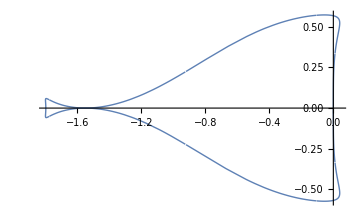
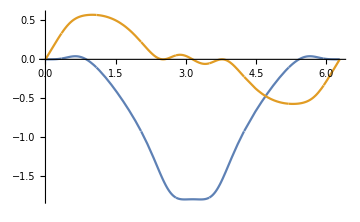
{-Graphics- -Graphics-,Null}

```mathematica
sol=NMinimize[{0.9 (-1/3+r[0] r[1]+5 r[0] r[2]+r[1] r[2]+13 r[0] r[3]+5 r[1] r[3]+r[2] r[3]+25 r[0] r[4]+13 r[1] r[4]+5 r[2] r[4]+r[3] r[4])^2+0.1 (r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2),cons},R];
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b]
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
Print["C"->Subscript[C, o+1]/σ[1]]
PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]
```

```mathematica
bs^2
```

(r[0]^2+r[1]^2+r[2]^2+r[3]^2+r[4]^2)^2

```mathematica
system={p'[x] == -2000p[x]+1000q[x]+1,q'[x] ==p[x]-q[x],p[0]==0,q[0]==0};
sol=DSolve[system, {p,q}, x] ;
sol[[1,1]]
```

p→Function[{x},(2 ⅇ^(-(2001 x)/2-(√4000001 x)/2-1/2 (-2001+√4000001) x) (-5999002 ⅇ^(√4000001 x)-1000 √4000001 ⅇ^(√4000001 x)-2001000 ⅇ^(2 √4000001 x)+1000 √4000001 ⅇ^(2 √4000001 x)+4000001 ⅇ^(1/2 (-2001+√4000001) x)-√4000001 ⅇ^(1/2 (-2001+√4000001) x)+4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x)+√4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x)-2001000 ⅇ^(1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)+1000 √4000001 ⅇ^(1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)+2001000 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)-1000 √4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)))/(4000001 (-2001+√4000001) (2001+√4000001))]

```mathematica
p=sol[[1,2,2,2]]
```

-((2 ⅇ^(-(2001 x)/2-(√4000001 x)/2-1/2 (-2001+√4000001) x) (4000002 ⅇ^(√4000001 x)+2000 √4000001 ⅇ^(√4000001 x)-ⅇ^(2 √4000001 x)+√4000001 ⅇ^(2 √4000001 x)-4000001 ⅇ^(1/2 (-2001+√4000001) x)+2001 √4000001 ⅇ^(1/2 (-2001+√4000001) x)-4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x)-2001 √4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x)+4000000 ⅇ^(1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)-2000 √4000001 ⅇ^(1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)+ⅇ^(√4000001 x+1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)-√4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)))/(4000001 (-2001+√4000001) (2001+√4000001)))

```mathematica
Plot[(2 ⅇ^(-(2001 x)/2-(√4000001 x)/2-1/2 (-2001+√4000001) x) (-5999002 ⅇ^(√4000001 x)-1000 √4000001 ⅇ^(√4000001 x)-2001000 ⅇ^(2 √4000001 x)+1000 √4000001 ⅇ^(2 √4000001 x)+4000001 ⅇ^(1/2 (-2001+√4000001) x)-√4000001 ⅇ^(1/2 (-2001+√4000001) x)+4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x)+√4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x)-2001000 ⅇ^(1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)+1000 √4000001 ⅇ^(1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)+2001000 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)-1000 √4000001 ⅇ^(√4000001 x+1/2 (-2001+√4000001) x+1/2 (2001+√4000001) x)))/(4000001 (-2001+√4000001) (2001+√4000001)),{x,0.05,0.5},PlotRange->All]
```

-Graphics-

```mathematica
NumberForm[0.,16]
```

0.

```mathematica
N[%257]
```

General::munfl: Exp[-8000.] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
p[t_]:={-2000q[t]+1000p[t]};
q[t_]:={p[t]-q[t]};
sol_function[t,xend]:={
h=xend/n,
(*alrb:*)
};
```